```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\cloudData\PhDWork\year2\bimBoundedSpectral\postProcess

```mathematica
Needs["MaTeX`"]
```

```mathematica
SetOptions[{Plot,ListPlot,LogPlot,LogLogPlot,ListLinePlot,ListLogLogPlot},Frame->True,Axes->False,GridLines->None,ImageSize->500,(*Apply the high-contrast colors and thickness*)PlotStyle->(Directive[AbsoluteThickness[1.5]]),(*Force deep black frame and tick numbers*)FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontSize->18],(*Base style for any text that isn't MaTeX*)BaseStyle->{FontFamily->"Latin Modern Roman 12",FontSize->18}];
```

```mathematica
SetOptions[MaTeX,"FontSize"->18];
```

```mathematica
litDat=ReadList["../outputData/mobParallelLiterature.txt",{Number,Number}];
```

```mathematica
bimDat=ReadList["../outputData/mobParallel.txt",Number];
```

```mathematica
fname=FileNames["../outputData/sccStructRBy6/vel*"]//AlphabeticSort
```

{..\outputData\sccStructRBy6\velL2p5.txt,..\outputData\sccStructRBy6\velL3.txt,..\outputData\sccStructRBy6\velL3p33.txt,..\outputData\sccStructRBy6\velL3p5.txt,..\outputData\sccStructRBy6\velL4.txt,..\outputData\sccStructRBy6\velL4p5.txt,..\outputData\sccStructRBy6\velL5.txt,..\outputData\sccStructRBy6\velL5p33.txt,..\outputData\sccStructRBy6\velL5p5.txt,..\outputData\sccStructRBy6\velL6.txt,..\outputData\sccStructRBy6\velL6p5.txt,..\outputData\sccStructRBy6\velL7.txt}

```mathematica
ixLst=Range[Length@fname]
```

{1,2,3,4,5,6,7,8,9,10,11,12}

```mathematica
bimSCCDat=Table[ReadList[fn,{Number,Number,Number}],{fn,fname}];
```

```mathematica
velSCCDat=bimSCCDat[[All,1,2]]
```

{-2.46164,-2.1865,-2.03892,-1.97135,-1.79133,-1.63784,-1.50496,-1.42626,-1.38955,-1.28758,-1.19693,-1.11582}

```mathematica
-1.3148267629147226/-0.926-1
```

0.419899

```mathematica
1.25/0.91-1
```

0.373626

#### Unbounded:

```mathematica
fnameUB=FileNames["../outputData/sccStructRBy6Unbounded/vel*"]//AlphabeticSort
```

{..\outputData\sccStructRBy6Unbounded\velL2p5.txt,..\outputData\sccStructRBy6Unbounded\velL3.txt,..\outputData\sccStructRBy6Unbounded\velL3p33.txt,..\outputData\sccStructRBy6Unbounded\velL3p5.txt,..\outputData\sccStructRBy6Unbounded\velL4.txt,..\outputData\sccStructRBy6Unbounded\velL4p5.txt,..\outputData\sccStructRBy6Unbounded\velL5.txt,..\outputData\sccStructRBy6Unbounded\velL5p33.txt,..\outputData\sccStructRBy6Unbounded\velL5p5.txt,..\outputData\sccStructRBy6Unbounded\velL6.txt,..\outputData\sccStructRBy6Unbounded\velL6p5.txt,..\outputData\sccStructRBy6Unbounded\velL7.txt}

```mathematica
ixLst=Range[Length@fnameUB]
```

{1,2,3,4,5,6,7,8,9,10,11,12}

```mathematica
bimSCCDatUB=Table[ReadList[fn,{Number,Number,Number}],{fn,fnameUB}];
```

```mathematica
velSCCDatUB=bimSCCDatUB[[All,1,2]]
```

{-3.07091,-2.80663,-2.66061,-2.59458,-2.41885,-2.26999,-2.14186,-2.06578,-2.03016,-1.93187,-1.84467,-1.76677}

```mathematica
velSCCDat//Dimensions
```

{12}

```mathematica
dist=Table[(k 0.5)/20,{k,0,35}];
```

```mathematica
litDat
```

{{0,0.888106},{0.0341981,0.888106},{0.0660377,0.888106},{0.100236,0.885756},{0.134434,0.885756},{0.166274,0.885756},{0.200472,0.883407},{0.23467,0.878708},{0.267689,0.876358},{0.300708,0.876358},{0.333726,0.871659},{0.366745,0.86931},{0.400943,0.86696},{0.433962,0.859912},{0.466981,0.852863},{0.501179,0.850514},{0.534198,0.841116},{0.568396,0.834068},{0.599057,0.82232},{0.633255,0.810573},{0.667453,0.801175},{0.700472,0.782379},{0.73467,0.758884},{0.767689,0.73304},{0.800708,0.695448},{0.833726,0.63906},{0.867925,0.568576},{0.899764,0.446402},{0.933962,0.218502}}

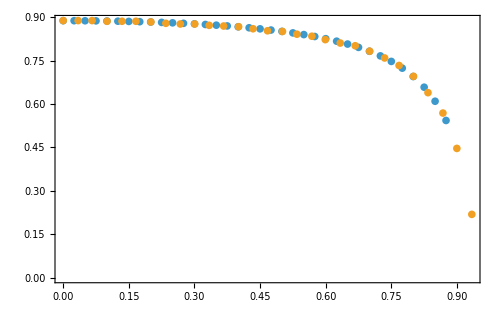

```mathematica
ListPlot[{Transpose[{dist,-bimDat}],litDat},PlotRange->All]
```

```mathematica
num=4/3 π (3 10^-3)^3(1.16-0.97)10^3 9.8
```

0.000210587

```mathematica
denom=6π 6000 10^-6 (3 10^-3)0.97 10^3
```

0.329113

```mathematica
vel=num/denom
```

0.000639863

```mathematica
vel 0.9159
```

0.00058605

```mathematica
1.744/(1 0.9159)
```

1.90414

#### Read mobility matrix from BIM output

```mathematica
nB=8;
```

```mathematica
fNamesOld=FileNames["../outputData/sccCrystal/mobMatL*.txt"]//AlphabeticSort
```

{..\outputData\sccCrystal\mobMatL2p5.txt,..\outputData\sccCrystal\mobMatL3.txt,..\outputData\sccCrystal\mobMatL3p33.txt,..\outputData\sccCrystal\mobMatL3p5.txt,..\outputData\sccCrystal\mobMatL4.txt,..\outputData\sccCrystal\mobMatL4p5.txt,..\outputData\sccCrystal\mobMatL5.txt,..\outputData\sccCrystal\mobMatL5p33.txt,..\outputData\sccCrystal\mobMatL5p5.txt,..\outputData\sccCrystal\mobMatL6.txt,..\outputData\sccCrystal\mobMatL6p5.txt,..\outputData\sccCrystal\mobMatL7.txt}

```mathematica
fNames=FileNames["../outputData/mob8S/mobMatL*.txt"]//AlphabeticSort
```

{..\outputData\mob8S\mobMatL2p5.txt,..\outputData\mob8S\mobMatL3.txt,..\outputData\mob8S\mobMatL3p33.txt,..\outputData\mob8S\mobMatL3p5.txt,..\outputData\mob8S\mobMatL4.txt,..\outputData\mob8S\mobMatL4p5.txt,..\outputData\mob8S\mobMatL5.txt,..\outputData\mob8S\mobMatL5p33.txt,..\outputData\mob8S\mobMatL5p5.txt,..\outputData\mob8S\mobMatL6.txt,..\outputData\mob8S\mobMatL6p5.txt,..\outputData\mob8S\mobMatL7.txt}

```mathematica
fNamesUB=FileNames["../outputData/sccCrystalUB/mobMatL*.txt"]//AlphabeticSort
```

{..\outputData\sccCrystalUB\mobMatL2p5.txt,..\outputData\sccCrystalUB\mobMatL3.txt,..\outputData\sccCrystalUB\mobMatL3p33.txt,..\outputData\sccCrystalUB\mobMatL3p5.txt,..\outputData\sccCrystalUB\mobMatL4.txt,..\outputData\sccCrystalUB\mobMatL4p5.txt,..\outputData\sccCrystalUB\mobMatL5.txt,..\outputData\sccCrystalUB\mobMatL5p33.txt,..\outputData\sccCrystalUB\mobMatL5p5.txt,..\outputData\sccCrystalUB\mobMatL6.txt,..\outputData\sccCrystalUB\mobMatL6p5.txt,..\outputData\sccCrystalUB\mobMatL7.txt}

```mathematica
mobDatOld=Table[ReadList[fNamesOld[[k]],Table[Number,nB 6]],{k,1,Length@fNamesOld}];
```

```mathematica
mobDat=Table[ReadList[fNames[[k]],Table[Number,nB 6]],{k,1,Length@fNames}];
```

```mathematica
mobDatUB=Table[ReadList[fNamesUB[[k]],Table[Number,nB 6]],{k,1,Length@fNamesUB}];
```

```mathematica
(*Chop[mobDat[[1]]-mobDat[[1]]^ᵀ,10^-5]//MatrixForm*)
```

```mathematica
mobDat//Dimensions
```

{12,48,48}

```mathematica
mobRef=Table[(mobDat[[k]]+Transpose[mobDat[[k]]])/2,{k,1,Length@mobDat}];
```

```mathematica
mobRefUB=Table[(mobDatUB[[k]]+Transpose[mobDatUB[[k]]])/2,{k,1,Length@mobDatUB}];
```

```mathematica
resMat=Table[Inverse[mobRef[[k]]],{k,1,Length@mobRef}];
```

```mathematica
resMatUB=Table[Inverse[mobRefUB[[k]]],{k,1,Length@mobRefUB}];
```

```mathematica
resMat[[1,1;;3 nB,1;;3nB]]//MatrixForm
```

(-2.10454 | -0.177689 | -0.178258 | 1.04675 | -0.180672 | -0.180968 | 0.252589 | -0.120565 | 0.247377 | 0.0494516 | -0.125282 | 0.180969 | 0.049715 | 0.181062 | -0.125627 | 0.252224 | 0.247505 | -0.120643 | 0.135964 | 0.134712 | 0.134276 | -0.0807341 | 0.121006 | 0.120636
-0.177689 | -2.10594 | -0.177849 | 0.180666 | 0.0481496 | -0.12529 | 0.120558 | -0.0824308 | 0.120559 | -0.125275 | 0.0479323 | 0.180846 | -0.181058 | 1.04526 | -0.181237 | 0.247504 | 0.25064 | -0.121004 | 0.134704 | 0.134142 | 0.134689 | -0.120999 | 0.250849 | 0.247723
-0.178258 | -0.177849 | -2.10456 | 0.180968 | -0.125295 | 0.0495485 | 0.247378 | -0.120559 | 0.252483 | -0.180968 | -0.180847 | 1.04678 | -0.125622 | 0.181233 | 0.0496004 | 0.120638 | 0.121 | -0.0806843 | 0.134276 | 0.13469 | 0.13594 | -0.120635 | 0.247723 | 0.252325
1.04675 | 0.180666 | 0.180968 | -2.10454 | 0.177686 | 0.178256 | 0.0494525 | 0.125282 | -0.180967 | 0.252588 | 0.120564 | -0.247377 | 0.252222 | -0.247502 | 0.120642 | 0.0497163 | -0.181057 | 0.125627 | -0.0807349 | -0.121004 | -0.120636 | 0.13596 | -0.134711 | -0.134276
-0.180672 | 0.0481496 | -0.125295 | 0.177686 | -2.10594 | -0.177851 | 0.125282 | 0.0479302 | 0.180848 | -0.120564 | -0.0824333 | 0.120563 | -0.247496 | 0.250639 | -0.121008 | 0.181054 | 1.04527 | -0.181239 | 0.121002 | 0.25085 | 0.247724 | -0.134708 | 0.134144 | 0.134693
-0.180968 | -0.12529 | 0.0495485 | 0.178256 | -0.177851 | -2.10456 | 0.180965 | -0.180848 | 1.04678 | -0.247375 | -0.120557 | 0.252483 | -0.120637 | 0.120997 | -0.0806841 | 0.125623 | 0.181235 | 0.0496011 | 0.120634 | 0.247724 | 0.252324 | -0.134274 | 0.134693 | 0.13594
0.252589 | 0.120558 | 0.247378 | 0.0494525 | 0.125282 | 0.180965 | -2.10454 | 0.177689 | -0.178258 | 1.04675 | 0.180664 | -0.180973 | 0.135963 | -0.134705 | 0.134279 | -0.0807351 | -0.121004 | 0.120638 | 0.0497188 | -0.181058 | -0.125623 | 0.252218 | -0.247495 | -0.120638
-0.120565 | -0.0824308 | -0.120559 | 0.125282 | 0.0479302 | -0.180848 | 0.177689 | -2.10594 | 0.177853 | -0.180676 | 0.0481492 | 0.125298 | -0.134707 | 0.134142 | -0.134698 | 0.120998 | 0.250851 | -0.247725 | 0.181059 | 1.04527 | 0.181235 | -0.247497 | 0.250636 | 0.121001
0.247377 | 0.120559 | 0.252483 | -0.180967 | 0.180848 | 1.04678 | -0.178258 | 0.177853 | -2.10455 | 0.18097 | 0.125296 | 0.0495483 | 0.134279 | -0.134692 | 0.135937 | -0.120638 | -0.247726 | 0.252316 | -0.125626 | -0.181238 | 0.049601 | 0.12064 | -0.121007 | -0.080684
0.0494516 | -0.125275 | -0.180968 | 0.252588 | -0.120564 | -0.247375 | 1.04675 | -0.180676 | 0.18097 | -2.10454 | -0.177688 | 0.178263 | -0.0807368 | 0.120998 | -0.120639 | 0.135963 | 0.13471 | -0.134279 | 0.252221 | 0.247505 | 0.120639 | 0.0497194 | 0.181053 | 0.125624
-0.125282 | 0.0479323 | -0.180847 | 0.120564 | -0.0824333 | -0.120557 | 0.180664 | 0.0481492 | 0.125296 | -0.177688 | -2.10594 | 0.177852 | -0.121005 | 0.250848 | -0.247725 | 0.13471 | 0.134143 | -0.134694 | 0.247501 | 0.250638 | 0.120999 | -0.181053 | 1.04527 | 0.181235
0.180969 | 0.180846 | 1.04678 | -0.247377 | 0.120563 | 0.252483 | -0.180973 | 0.125298 | 0.0495483 | 0.178263 | 0.177852 | -2.10455 | 0.120636 | -0.247724 | 0.252317 | -0.134278 | -0.134695 | 0.135937 | -0.120642 | -0.121006 | -0.0806841 | 0.125626 | -0.181239 | 0.0496007
0.049715 | -0.181058 | -0.125622 | 0.252222 | -0.247496 | -0.120637 | 0.135963 | -0.134707 | 0.134279 | -0.0807368 | -0.121005 | 0.120636 | -2.10454 | 0.17769 | -0.178262 | 1.04675 | 0.180665 | -0.180974 | 0.252588 | 0.120558 | 0.247379 | 0.0494536 | 0.125282 | 0.180968
0.181062 | 1.04526 | 0.181233 | -0.247502 | 0.250639 | 0.120997 | -0.134705 | 0.134142 | -0.134692 | 0.120998 | 0.250848 | -0.247724 | 0.17769 | -2.10594 | 0.177851 | -0.180674 | 0.0481451 | 0.125296 | -0.12056 | -0.0824346 | -0.120557 | 0.125277 | 0.0479303 | -0.180847
-0.125627 | -0.181237 | 0.0496004 | 0.120642 | -0.121008 | -0.0806841 | 0.134279 | -0.134698 | 0.135937 | -0.120639 | -0.247725 | 0.252317 | -0.178262 | 0.177851 | -2.10456 | 0.180971 | 0.125297 | 0.0495474 | 0.24738 | 0.120563 | 0.252484 | -0.180968 | 0.180848 | 1.04678
0.252224 | 0.247504 | 0.120638 | 0.0497163 | 0.181054 | 0.125623 | -0.0807351 | 0.120998 | -0.120638 | 0.135963 | 0.13471 | -0.134278 | 1.04675 | -0.180674 | 0.180971 | -2.10454 | -0.177689 | 0.178264 | 0.0494487 | -0.125276 | -0.180968 | 0.252589 | -0.120564 | -0.247377
0.247505 | 0.25064 | 0.121 | -0.181057 | 1.04527 | 0.181235 | -0.121004 | 0.250851 | -0.247726 | 0.13471 | 0.134143 | -0.134695 | 0.180665 | 0.0481451 | 0.125297 | -0.177689 | -2.10594 | 0.177853 | -0.125283 | 0.0479296 | -0.180847 | 0.120564 | -0.0824339 | -0.120559
-0.120643 | -0.121004 | -0.0806843 | 0.125627 | -0.181239 | 0.0496011 | 0.120638 | -0.247725 | 0.252316 | -0.134279 | -0.134694 | 0.135937 | -0.180974 | 0.125296 | 0.0495474 | 0.178264 | 0.177853 | -2.10455 | 0.180965 | 0.180847 | 1.04678 | -0.247375 | 0.120562 | 0.252484
0.135964 | 0.134704 | 0.134276 | -0.0807349 | 0.121002 | 0.120634 | 0.0497188 | 0.181059 | -0.125626 | 0.252221 | 0.247501 | -0.120642 | 0.252588 | -0.12056 | 0.24738 | 0.0494487 | -0.125283 | 0.180965 | -2.10453 | -0.177691 | -0.178254 | 1.04675 | -0.180669 | -0.180968
0.134712 | 0.134142 | 0.13469 | -0.121004 | 0.25085 | 0.247724 | -0.181058 | 1.04527 | -0.181238 | 0.247505 | 0.250638 | -0.121006 | 0.120558 | -0.0824346 | 0.120563 | -0.125276 | 0.0479296 | 0.180847 | -0.177691 | -2.10594 | -0.17785 | 0.180666 | 0.0481495 | -0.125293
0.134276 | 0.134689 | 0.13594 | -0.120636 | 0.247724 | 0.252324 | -0.125623 | 0.181235 | 0.049601 | 0.120639 | 0.120999 | -0.0806841 | 0.247379 | -0.120557 | 0.252484 | -0.180968 | -0.180847 | 1.04678 | -0.178254 | -0.17785 | -2.10456 | 0.180966 | -0.125295 | 0.0495478
-0.0807341 | -0.120999 | -0.120635 | 0.13596 | -0.134708 | -0.134274 | 0.252218 | -0.247497 | 0.12064 | 0.0497194 | -0.181053 | 0.125626 | 0.0494536 | 0.125277 | -0.180968 | 0.252589 | 0.120564 | -0.247375 | 1.04675 | 0.180666 | 0.180966 | -2.10454 | 0.177684 | 0.178256
0.121006 | 0.250849 | 0.247723 | -0.134711 | 0.134144 | 0.134693 | -0.247495 | 0.250636 | -0.121007 | 0.181053 | 1.04527 | -0.181239 | 0.125282 | 0.0479303 | 0.180848 | -0.120564 | -0.0824339 | 0.120562 | -0.180669 | 0.0481495 | -0.125295 | 0.177684 | -2.10594 | -0.177851
0.120636 | 0.247723 | 0.252325 | -0.134276 | 0.134693 | 0.13594 | -0.120638 | 0.121001 | -0.080684 | 0.125624 | 0.181235 | 0.0496007 | 0.180968 | -0.180847 | 1.04678 | -0.247377 | -0.120559 | 0.252484 | -0.180968 | -0.125293 | 0.0495478 | 0.178256 | -0.177851 | -2.10456)

```mathematica
matLst=Table[Flatten[Partition[resMat[[k,1;;3 nB,1;;3nB]],{3,3}],1],{k,1,Length@mobRef}];
```

```mathematica
matLstUB=Table[Flatten[Partition[resMatUB[[k,1;;3 nB,1;;3nB]],{3,3}],1],{k,1,Length@mobRefUB}];
```

```mathematica
Rsum=Table[Sum[matLst[[k,l]],{l,1,Length@matLst[[k]]}],{k,1,Length@matLst}];(*k index runs over different lattice spacings.*)
Rsum[[2]]//MatrixForm
```

(-3.59346 | -0.0000216725 | -0.000012195
-0.0000216725 | -3.72326 | 0.0000247753
-0.000012195 | 0.0000247753 | -3.59335)

```mathematica
RsumUB=Table[Sum[matLstUB[[k,l]],{l,1,Length@matLstUB[[k]]}],{k,1,Length@matLstUB}];(*k index runs over different lattice spacings.*)
RsumUB[[2]]//MatrixForm
```

(-2.90665 | 6.1772×10^-7 | 2.03263×10^-7
6.1772×10^-7 | -2.90665 | 1.17165×10^-6
2.03263×10^-7 | 1.17165×10^-6 | -2.90664)

```mathematica
matLst[[1]]//Dimensions
```

{64,3,3}

```mathematica
dragCoeff=Rsum[[All,2,2]]
```

{-3.29119,-3.72326,-4.00057,-4.14079,-4.54197,-4.92511,-5.28916,-5.51871,-5.63359,-5.95836,-6.26361,-6.54966}

```mathematica
dragCoeffUB=RsumUB[[All,2,2]]
```

{-2.63495,-2.90665,-3.07612,-3.15753,-3.38883,-3.60179,-3.79782,-3.9198,-3.97836,-4.1449,-4.29878,-4.44127}

```mathematica
vFall=-8/dragCoeff
```

{2.43073,2.14865,1.99972,1.932,1.76135,1.62433,1.51253,1.44961,1.42005,1.34265,1.27722,1.22144}

```mathematica
vFallUB=-8/dragCoeffUB
```

{3.03611,2.75231,2.60068,2.53363,2.3607,2.22112,2.10647,2.04092,2.01088,1.93008,1.86099,1.80129}

```mathematica
(*expDat={{1.9943138510370522,2.603776999662809},
{2.3240559229138142,2.0275896677745746},
{2.663360003008471,1.7130779687711408},
{2.9933061428018304,1.5116988106333347},
{3.3271529277012015,1.2429550008085057},
{3.6572101329154907,1.0732428576080104},
{3.9922231549663376,0.916680172084238},
{4.321876308863974,0.7578257489032785},
{4.652869451414732,0.619723702416392},
{5.325920152528611,0.4077288575297677},
{6.32153662648955,0.22297578351099068},
{6.667246569771301,0.1308705579514683}
};*)
```

```mathematica
expDat={
{2.0031284426547122,1.9335866385981855},
{2.3347071442459075,1.6071655610737032},
{2.6685223676311822,1.4174742006559518},
{3.0004180475783717,1.2810786123620808},
{3.339492185891032,1.091135698535988},
{3.670697147756831,0.989588285210876},
{4.003341479322156,0.8667198932627369},
{4.338918369891544,0.7485872072891563},
{4.673315310688152,0.6443041209516118},
{5.341503714691428,0.4625423388046464},
{6.338601956988526,0.2808567087710062},
{6.674124225508587,0.18095713485806605}};
```

```mathematica
dList=Table[k,{k,2.5,7,0.5}];
dList=Join[dList,{3.33,5.33}]//Sort
```

{2.5,3.,3.33,3.5,4.,4.5,5.,5.33,5.5,6.,6.5,7.}

```mathematica
dList//Dimensions
```

{12}

```mathematica
vel
vel 0.9159 (*6000cSt*)
(*vel 0.945 (*6000cSt*)*)
```

0.000639863

0.00058605

```mathematica
vSngl=0.9236
```

0.9236

```mathematica
dSccLst=Table[k,{k,2.5,7,0.5}]
```

{2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.}

```mathematica
(*dSccLst=Table[k,{k,3,7,0.5}]*)
```

```mathematica
1.2555/0.913-1
```

0.375137

```mathematica
dat1=Transpose[{dList,vFall/vSngl-1}]
dat2=Transpose[{dList,-velSCCDat/vSngl-1}]
dat3=Transpose[{dList,-velSCCDatUB[[ixLst]]/1-1}]
```

{{2.5,1.6318},{3.,1.32639},{3.33,1.16513},{3.5,1.09181},{4.,0.907047},{4.5,0.758693},{5.,0.637643},{5.33,0.569526},{5.5,0.537519},{6.,0.453716},{6.5,0.382871},{7.,0.322475}}

{{2.5,1.66527},{3.,1.36737},{3.33,1.20758},{3.5,1.13441},{4.,0.939508},{4.5,0.773323},{5.,0.629448},{5.33,0.544239},{5.5,0.504495},{6.,0.394091},{6.5,0.295943},{7.,0.208121}}

{{2.5,2.07091},{3.,1.80663},{3.33,1.66061},{3.5,1.59458},{4.,1.41885},{4.5,1.26999},{5.,1.14186},{5.33,1.06578},{5.5,1.03016},{6.,0.931872},{6.5,0.844671},{7.,0.76677}}

```mathematica
dat4=Transpose[{dList,vFallUB-1}]
```

{{2.5,2.03611},{3.,1.75231},{3.33,1.60068},{3.5,1.53363},{4.,1.3607},{4.5,1.22112},{5.,1.10647},{5.33,1.04092},{5.5,1.01088},{6.,0.930083},{6.5,0.860991},{7.,0.801286}}

```mathematica
-(0.8766292350007256+1)0.9159
```

-1.7188

```mathematica
1.7188/0.9159-1
```

0.876624

```mathematica
Export["./figs/only8Spheres.txt",dat1,"Table"]
```

./figs/only8Spheres.txt

```mathematica
Export["./figs/only8SpheresUnBounded.txt",dat4,"Table"]
```

./figs/only8SpheresUnBounded.txt

```mathematica
Export["./figs/sccBounded.txt",dat2,"Table"]
```

./figs/sccBounded.txt

```mathematica
Export["./figs/sccUnBounded.txt",dat3,"Table"]
```

./figs/sccUnBounded.txt

```mathematica
Integrate[Sin[t]^2,{t,0,2π}]
```

π

```mathematica
Integrate[Sin[t] Cos[t]^2,{t,0,π}]
```

2/3

```mathematica
Integrate[Sin[t]^3,{t,0,π}]
```

4/3

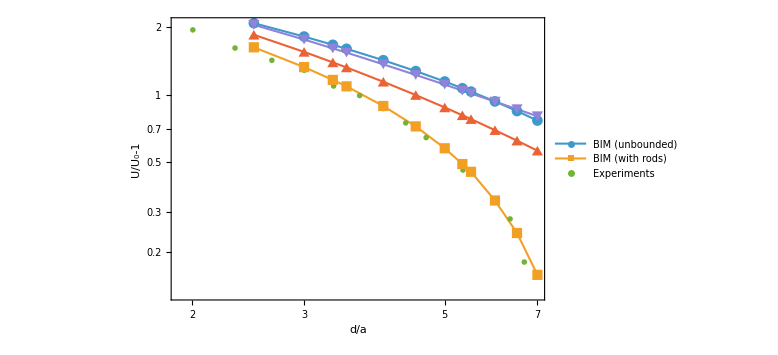

```mathematica
ListLogLogPlot[{Transpose[{dList,-velSCCDatUB[[ixLst]]/1-1}],Transpose[{dList,-velSCCDat[[ixLst]]/0.9159-1}],expDat,dat1,dat4},PlotMarkers->{Automatic,Automatic,"OpenMarkers"},Joined->{True,True,False},Frame->True,FrameLabel->{"d/a","U/U_0-1"},LabelStyle->{Black,Directive[24]},ImageSize->Large,PlotLegends->{"BIM (unbounded)","BIM (with rods)","Experiments"},GridLines->Automatic]
```

```mathematica
dat2[[All,2]]+0.05
```

{1.74984,1.45219,1.29781,1.22448,1.0254,0.85961,0.714862,0.628934,0.588954,0.47916,0.381031,0.292088}

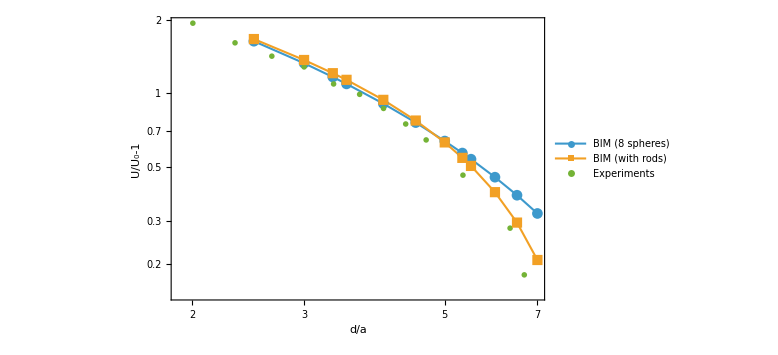

```mathematica
ListLogLogPlot[{dat1[[1;;-1]],dat2,expDat(*,Transpose[{dat2[[All,1]],dat2[[All,2]]+0.04}],Transpose[{dat2[[All,1]],dat2[[All,2]]-0.04}]*)},PlotMarkers->{Automatic,Automatic,"OpenMarkers",None,None},Joined->{True,True,False,True,True},Frame->True,FrameLabel->{"d/a","U/U_0-1"},LabelStyle->{Black,Directive[24]},ImageSize->Large,PlotLegends->{"BIM (8 spheres)","BIM (with rods)","Experiments"},GridLines->Automatic]
```

#### For capped cylinder:

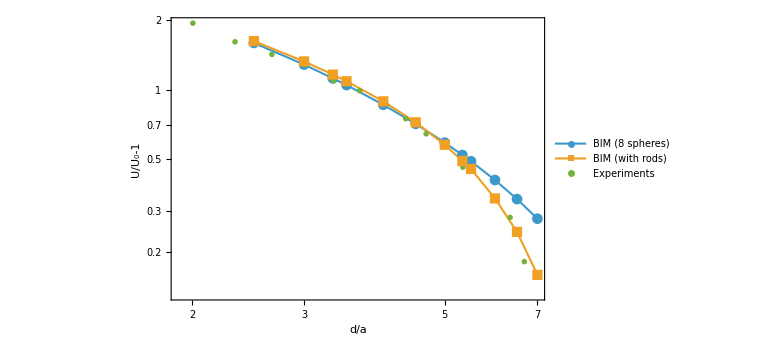

```mathematica
ListLogLogPlot[{Transpose[{dList,vFall/0.9159-1}],Transpose[{dList,-velSCCDat[[ixLst]]/0.9159-1}],expDat},PlotMarkers->{Automatic,Automatic,"OpenMarkers"},Joined->{True,True,False},Frame->True,FrameLabel->{"d/a","U/U_0-1"},LabelStyle->{Black,Directive[24]},ImageSize->Large,PlotLegends->{"BIM (8 spheres)","BIM (with rods)","Experiments"},GridLines->Automatic]
```

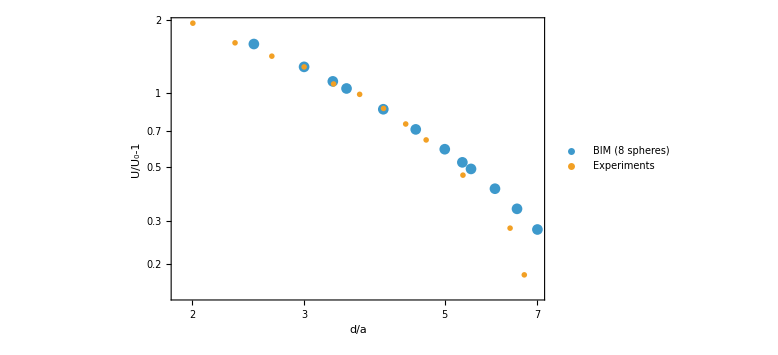

```mathematica
ListLogLogPlot[{Transpose[{dList,vFall/0.9159-1}](*,Transpose[{dList,vFall-1}]*),expDat},PlotMarkers->{Automatic,"OpenMarkers"},Frame->True,FrameLabel->{"d/a","U/U_0-1"},LabelStyle->{Black,Directive[24]},ImageSize->Large,PlotLegends->{"BIM (8 spheres)","Experiments"},GridLines->Automatic]
```

```mathematica
vFac=0.9159;
```

```mathematica
dList
vFall
```

{2.5,3.,3.33,3.5,4.,4.5,5.,5.33,5.5,6.,6.5,7.}

{2.37134,2.08981,1.93988,1.87374,1.70356,1.56756,1.45664,1.39376,1.36512,1.28877,1.22447,1.1699}

```mathematica
-velSCCDat/0.9159-1
```

{1.61869,1.3225,1.16055,1.08659,0.889389,0.722174,0.577603,0.491892,0.454409,0.339101,0.243277,0.158743}

```mathematica
phiS[d_]:=(8 4/3 π+12 π (1/6)^2(d-2))/(d^3+6 d^2+1/2 6π d+4/3 π)
```

```mathematica
mStr[d_]:=(8+12 (1/6)^2(d-2));
```

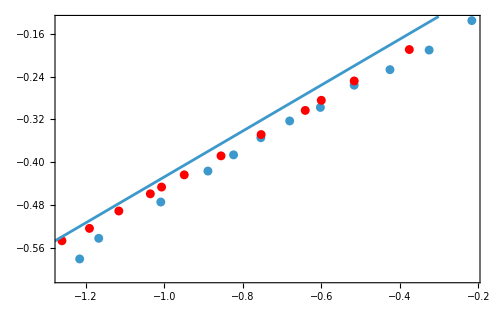

```mathematica
Show[ListPlot[Transpose[{phiS[expDat[[All,1]]],(expDat[[All,2]]+1)/mStr[expDat[[All,1]]]^(2/3)}],ScalingFunctions->{"Log10","Log10"}],ListPlot[Transpose[{phiS[dList],(vFall/vFac)/mStr[expDat[[All,1]]]^(2/3)}],ScalingFunctions->{"Log10","Log10"},PlotStyle->Red],Plot[0.3{ 0.06^-0.43 x^0.43},{x,0.02,0.5},ScalingFunctions->{"Log10","Log10"}]]
```

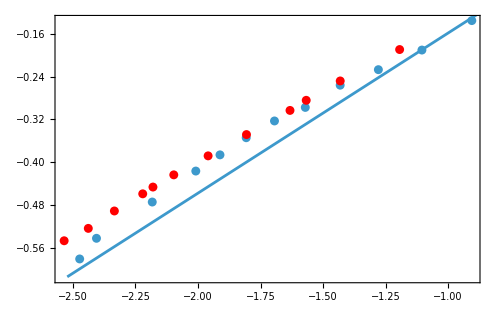

```mathematica
Show[ListPlot[Transpose[{expDat[[All,1]]^-3,(expDat[[All,2]]+1)/mStr[expDat[[All,1]]]^(2/3)}],ScalingFunctions->{"Log10","Log10"}],ListPlot[Transpose[{dList^-3,(vFall/vFac)/mStr[expDat[[All,1]]]^(2/3)}],ScalingFunctions->{"Log10","Log10"},PlotStyle->Red],Plot[0.2{ 0.003^(-1/3)x^0.3},{x,0.003,0.5},ScalingFunctions->{"Log10","Log10"}]]
```

```mathematica
(*Manipulate[Plot[{x^(1/3)+ k x^(2/3),x^(1/3)},{x,0.02,0.5},ScalingFunctions->{"Log10","Log10"},PlotRange->{0,5}],{k,0,10}]*)
```

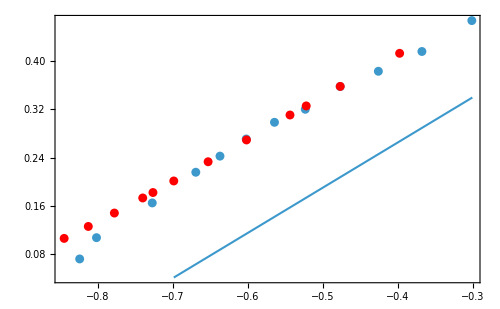

```mathematica
Show[ListPlot[Transpose[{expDat[[All,1]]^-1,(expDat[[All,2]]+1)}],ScalingFunctions->{"Log10","Log10"}],ListPlot[Transpose[{dList^-1,(vFall/vFac)}],ScalingFunctions->{"Log10","Log10"},PlotStyle->Red],Plot[1.1{ 0.2^(-3/4)x^(3/4)},{x,0.2,0.5},ScalingFunctions->{"Log10","Log10"}]]
```

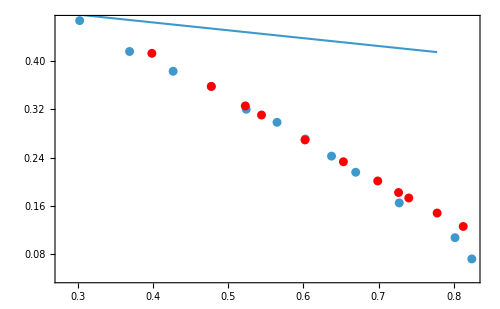

```mathematica
Show[ListPlot[Transpose[{expDat[[All,1]],(expDat[[All,2]]+1)}],ScalingFunctions->{"Log10","Log10"}],ListPlot[Transpose[{dList,(vFall/vFac)}],ScalingFunctions->{"Log10","Log10"},PlotStyle->Red],Plot[3{ 2^0.13 x^-0.13},{x,2,6},ScalingFunctions->{"Log10","Log10"}]]
```

#### Get force and torque required to produce RBM (needed for velocity field generation in BIM):

```mathematica
vGen=Table[Join[Table[{0,vFall[[k]],0},nB],Table[{0,0,0},nB]],{k,1,Length@dList}];
vGen//Dimensions
```

{12,16,3}

```mathematica
vGen[[7]]
```

{{0,1.45664,0},{0,1.45664,0},{0,1.45664,0},{0,1.45664,0},{0,1.45664,0},{0,1.45664,0},{0,1.45664,0},{0,1.45664,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
fConstr=-Table[Partition[resMat[[k]].Flatten[vGen[[k]]],3],{k,1,Length@vGen}];
```

```mathematica
fConstr[[2]]
```

{{-0.170286,0.999999,-0.170336},{0.170265,1.,-0.17033},{0.170261,1.,0.170333},{-0.170267,0.999999,0.170356},{0.170314,1.,0.170334},{-0.170287,0.999999,0.170358},{-0.170257,0.999998,-0.170342},{0.170256,1.,-0.170332},{0.167478,2.88196×10^-6,-0.167479},{0.167476,4.38823×10^-6,0.167479},{-0.167478,-6.86964×10^-6,0.16748},{-0.167477,-2.38999×10^-6,-0.167482},{0.167494,6.75735×10^-6,-0.167477},{0.167477,1.26834×10^-6,0.167484},{-0.167477,-2.91223×10^-6,0.167484},{-0.167475,-9.0884×10^-7,-0.167478}}

```mathematica
dList[[1]]
```

2.5

```mathematica
fNamesFT={"../outputData/Freq/FTd2p5.txt","../outputData/Freq/FTd3.txt","../outputData/Freq/FTd3p33.txt","../outputData/Freq/FTd3p5.txt","../outputData/Freq/FTd4.txt","../outputData/Freq/FTd4p5.txt","../outputData/Freq/FTd5.txt","../outputData/Freq/FTd5p33.txt","../outputData/Freq/FTd5p5.txt","../outputData/Freq/FTd6.txt","../outputData/Freq/FTd6p5.txt","../outputData/Freq/FTd7.txt"};
```

```mathematica
Do[
Export[fNamesFT[[k]],fConstr[[k]],"Table"]
,{k,1,Length@fConstr}]
```

#### Read velocity field in xy plane from BIM results:

```mathematica
vdat={ReadList["../outputData/sccStructRBy6/uFieldL3p33.txt",Table[Number,6]],ReadList["../outputData/sccStructRBy6/uFieldL4.txt",Table[Number,6]],ReadList["../outputData/sccStructRBy6/uFieldL5p33.txt",Table[Number,6]](*,ReadList["../outputData/sccStructRBy6/uField5p5.txt",Table[Number,6]]*)};
vdat[[1]]//Dimensions
```

{16683,6}

```mathematica
20/3//N
```

6.66667

```mathematica
6.5 3
```

19.5

```mathematica
10/3.333
```

```mathematica
vdat[[3]]//Dimensions
```

{26643,6}

```mathematica
vdat[[1,1]]
```

{-24.8,-6.666,0.,-0.00814657,-0.00234647,2.66341×10^-6}

```mathematica
nxpt=Floor[49.6/0.2]
```

248

```mathematica
vfieldDat=Table[Partition[vdat[[k]],nxpt+1],{k,1,Length@vdat}];
```

```mathematica
(*vfieldDat[[2]]*)
```

```mathematica
vPlotDat=Table[Partition[vdat[[1,k]],3][[1;;2,1;;2]],{k,1,Length@vdat[[1]]}];
```

```mathematica
vPlotDat[[nxpt/2-10;;nxpt/2+10]]
```

{{{-2.2,-6.6666},{0.0995976,0.465331}},{{-2.,-6.6666},{0.0920849,0.476202}},{{-1.8,-6.6666},{0.0841144,0.486211}},{{-1.6,-6.6666},{0.0757351,0.495295}},{{-1.4,-6.6666},{0.0669984,0.503402}},{{-1.2,-6.6666},{0.0579566,0.51049}},{{-1.,-6.6666},{0.0486611,0.516528}},{{-0.8,-6.6666},{0.0391613,0.521491}},{{-0.6,-6.6666},{0.0295035,0.525364}},{{-0.4,-6.6666},{0.0197309,0.528136}},{{-0.2,-6.6666},{0.0098838,0.529802}},{{0.,-6.6666},{-5.14318×10^-9,0.530357}},{{0.2,-6.6666},{-0.00988381,0.529802}},{{0.4,-6.6666},{-0.0197309,0.528136}},{{0.6,-6.6666},{-0.0295035,0.525364}},{{0.8,-6.6666},{-0.0391613,0.521491}},{{1.,-6.6666},{-0.0486611,0.516528}},{{1.2,-6.6666},{-0.0579566,0.51049}},{{1.4,-6.6666},{-0.0669984,0.503402}},{{1.6,-6.6666},{-0.0757351,0.495295}},{{1.8,-6.6666},{-0.0841144,0.486211}}}

```mathematica
strmPlt=Show[ListStreamPlot[-vPlotDat,AspectRatio->Automatic,StreamMarkers->"Drop",ClippingStyle->Automatic],FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontSize->16],(*Base style for any text that isn't MaTeX*)BaseStyle->{FontFamily->"Latin Modern Roman 12",FontSize->16}]
```

-Graphics-

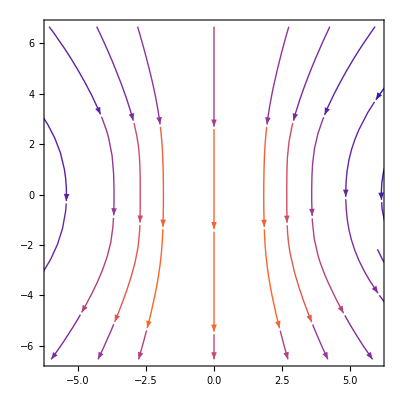

```mathematica
Show[ListStreamPlot[-vPlotDat,ClippingStyle->Automatic,PlotRange->{{-6,6},All},FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontSize->16],(*Base style for any text that isn't MaTeX*)BaseStyle->{FontFamily->"Latin Modern Roman 12",FontSize->16}]]
```

```mathematica
Cuboid[]
```

Cuboid[{0,0,0}]

```mathematica
aL=5.5;
```

```mathematica
Graphics3D[{Table[Sphere[{pm1 aL/2,pm2 aL/2,pm3 aL/2}],{pm1,-1,1,2},{pm2,-1,1,2},{pm3,-1,1,2}],
Table[Cylinder[{{-aL/2,pm aL/2,pm2 aL/2},{aL/2,pm aL/2,pm2 aL/2}},1/6],{pm,-1,1,2},{pm2,-1,1,2}],
Table[Cylinder[{{pm aL/2,- aL/2,pm2 aL/2},{pm aL/2, aL/2,pm2 aL/2}},1/6],{pm,-1,1,2},{pm2,-1,1,2}],
Table[Cylinder[{{pm aL/2,pm2 aL/2,- aL/2},{pm aL/2,pm2  aL/2, aL/2}},1/6],{pm,-1,1,2},{pm2,-1,1,2}],
Cuboid[{-aL,-aL,0},{aL,aL,0}]
}]
```

-Graphics3D-

```mathematica
plot3D=Graphics3D[strmPlt[[1]]/. {x_Real,y_Real}:>{x,y,0.1}];
```

```mathematica
strtPlt=Graphics3D[{Opacity[0.4],Cuboid[{-25,-6,0},{25,6,0}],Opacity[1],Blue,Table[Sphere[{pm1 aL/2,pm2 aL/2,pm3 aL/2}],{pm1,-1,1,2},{pm2,-1,1,2},{pm3,-1,1,2}],
Table[Cylinder[{{-aL/2,pm aL/2,pm2 aL/2},{aL/2,pm aL/2,pm2 aL/2}},1/6],{pm,-1,1,2},{pm2,-1,1,2}],
Table[Cylinder[{{pm aL/2,- aL/2,pm2 aL/2},{pm aL/2, aL/2,pm2 aL/2}},1/6],{pm,-1,1,2},{pm2,-1,1,2}],
Table[Cylinder[{{pm aL/2,pm2 aL/2,- aL/2},{pm aL/2,pm2  aL/2, aL/2}},1/6],{pm,-1,1,2},{pm2,-1,1,2}]
}]
```

-Graphics3D-

```mathematica
Show[strtPlt,
plot3D,PlotRange->All,BoxRatios->Automatic,Axes->True,AxesLabel->{"X","Y","Z"}
]
```

```mathematica
Show[Graphics3D[{Opacity[0.4],Cuboid[{-25,-6,0},{25,6,0}],Opacity[1],Blue,Table[Sphere[{pm1 aL/2,pm2 aL/2,pm3 aL/2}],{pm1,-1,1,2},{pm2,-1,1,2},{pm3,-1,1,2}],
Table[Cylinder[{{-aL/2,pm aL/2,pm2 aL/2},{aL/2,pm aL/2,pm2 aL/2}},1/6],{pm,-1,1,2},{pm2,-1,1,2}],
Table[Cylinder[{{pm aL/2,- aL/2,pm2 aL/2},{pm aL/2, aL/2,pm2 aL/2}},1/6],{pm,-1,1,2},{pm2,-1,1,2}],
Table[Cylinder[{{pm aL/2,pm2 aL/2,- aL/2},{pm aL/2,pm2  aL/2, aL/2}},1/6],{pm,-1,1,2},{pm2,-1,1,2}],
strmPlt[[1]]/. Arrow[z_]:>Arrow[z/. {x_Real,y_Real}:>{x,y,0}]
}],
PlotRange->All,BoxRatios->Automatic,Axes->True,AxesLabel->{MaTeX["Y"],MaTeX["Z"],MaTeX["X"]},FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontSize->16],(*Base style for any text that isn't MaTeX*)BaseStyle->{FontFamily->"Latin Modern Roman 12",FontSize->16},ImageSize->Large]
```

-Graphics3D-

```mathematica
nyPt=Table[Floor[4 aL/0.2],{aL,{3.3333,4,5.3333}}]
```

{66,80,106}

```mathematica
vfieldDat[[1,nyPt[[1]]/2+1,nxpt/2+51]]
```

{10.,-0.066,0.,-0.00151169,0.00415846,-2.20171×10^-7}

```mathematica
dFieldLst={3.3333,4,5.3333};
```

```mathematica
1.5 dFieldLst
```

{4.99995,6.,7.99995}

```mathematica
vfieldDat//Dimensions
```

{3}

```mathematica
vfieldDat[[1,1,5]]
```

{-24.,-6.6666,0.,-0.00213637,-0.0165316,-3.55021×10^-6}

```mathematica
maxV=Table[Max@vfieldDat[[k,nyPt[[2]]/2+1,1;;nxpt,5]],{k,1,Length@vfieldDat}]
```

{0.978962,0.919338,42.2336}

```mathematica
dFew={3.33,4,5.33,5.5};
```

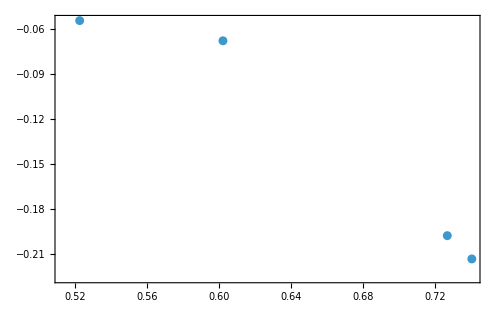

```mathematica
ListPlot[Transpose[{dFew,maxV}],ScalingFunctions->{"Log10","Log10"}]
```

```mathematica
(0.634-0.612)/(5.5-5.33)
```

0.129412

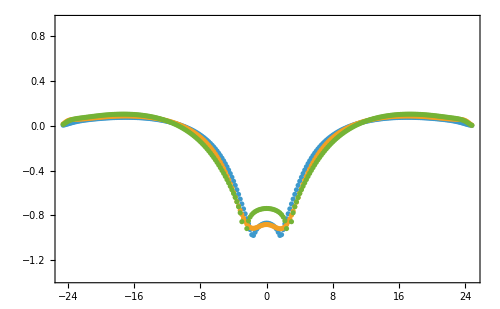

```mathematica
ListPlot[-{vfieldDat[[1,nyPt[[2]]/2+1,1;;nxpt,1;;5;;4]],vfieldDat[[2,nyPt[[2]]/2+1,1;;nxpt,1;;5;;4]],vfieldDat[[3,nyPt[[2]]/2+1,1;;nxpt,1;;5;;4]](*,vfieldDat[[4,nyPt[[2]]/2+1,1;;nxpt,1;;5;;4]]*)}]
```

```mathematica
vfieldDat[[2,nyPt[[2]]/2+1,nxpt/2-39;;nxpt/2+41,1;;5;;4]]
```

{{-8.,0.105094},{-7.8,0.117991},{-7.6,0.131701},{-7.4,0.146288},{-7.2,0.161818},{-7.,0.178362},{-6.8,0.195998},{-6.6,0.214807},{-6.4,0.234878},{-6.2,0.256301},{-6.,0.279169},{-5.8,0.303577},{-5.6,0.329616},{-5.4,0.357369},{-5.2,0.386907},{-5.,0.418278},{-4.8,0.451496},{-4.6,0.486529},{-4.4,0.523282},{-4.2,0.561574},{-4.,0.601122},{-3.8,0.641512},{-3.6,0.682186},{-3.4,0.722431},{-3.2,0.761376},{-3.,0.798019},{-2.8,0.831287},{-2.6,0.860126},{-2.4,0.883635},{-2.2,0.901219},{-2.,0.912724},{-1.8,0.918494},{-1.6,0.919338},{-1.4,0.916388},{-1.2,0.910916},{-1.,0.904161},{-0.8,0.897204},{-0.6,0.890911},{-0.4,0.88592},{-0.2,0.882663},{0.,0.881382},{0.2,0.882156},{0.4,0.884904},{0.6,0.88938},{0.8,0.895152},{1.,0.901583},{1.2,0.90781},{1.4,0.912759},{1.6,0.915204},{1.8,0.913885},{2.,0.907685},{2.2,0.895813},{2.4,0.877934},{2.6,0.854211},{2.8,0.82524},{3.,0.791918},{3.2,0.755293},{3.4,0.716428},{3.6,0.676314},{3.8,0.635808},{4.,0.595616},{4.2,0.556287},{4.4,0.518223},{4.6,0.481705},{4.8,0.446906},{5.,0.413919},{5.2,0.382774},{5.4,0.353452},{5.6,0.325906},{5.8,0.300064},{6.,0.275842},{6.2,0.253149},{6.4,0.231892},{6.6,0.211976},{6.8,0.193312},{7.,0.175813},{7.2,0.159397},{7.4,0.143987},{7.6,0.129512},{7.8,0.115907},{8.,0.103109}}

```mathematica
vAllPlot={vfieldDat[[1,nyPt[[1]]/2+1,nxpt/2-24;;nxpt/2+26,1;;5;;4]],
vfieldDat[[2,nyPt[[2]]/2+1,nxpt/2-29;;nxpt/2+31,1;;5;;4]],
vfieldDat[[3,nyPt[[3]]/2+1,nxpt/2-39;;nxpt/2+41,1;;5;;4]]};
```

```mathematica
vAllPlot[[1,All,1]]/dFieldLst[[1]]
```

{-1.50002,-1.44001,-1.38001,-1.32001,-1.26001,-1.20001,-1.14001,-1.08001,-1.02001,-0.96001,-0.900009,-0.840008,-0.780008,-0.720007,-0.660007,-0.600006,-0.540005,-0.480005,-0.420004,-0.360004,-0.300003,-0.240002,-0.180002,-0.120001,-0.0600006,0.,0.0600006,0.120001,0.180002,0.240002,0.300003,0.360004,0.420004,0.480005,0.540005,0.600006,0.660007,0.720007,0.780008,0.840008,0.900009,0.96001,1.02001,1.08001,1.14001,1.20001,1.26001,1.32001,1.38001,1.44001,1.50002}

```mathematica
vAllPlot[[1,All,2]]
```

{0.351371,0.381757,0.414419,0.449447,0.48688,0.526679,0.568691,0.61261,0.657931,0.703913,0.749555,0.793605,0.834613,0.871045,0.901467,0.924767,0.940405,0.948584,0.950276,0.94704,0.940702,0.933042,0.925575,0.91946,0.915489,0.914115,0.915489,0.91946,0.925575,0.933042,0.940702,0.94704,0.950276,0.948584,0.940405,0.924767,0.901467,0.871045,0.834613,0.793605,0.749555,0.703913,0.657931,0.61261,0.568691,0.526679,0.48688,0.449447,0.414419,0.381757,0.351371}

```mathematica
vAllPlot[[1]]
```

{{-5.,0.351371},{-4.8,0.381757},{-4.6,0.414419},{-4.4,0.449447},{-4.2,0.48688},{-4.,0.526679},{-3.8,0.568691},{-3.6,0.61261},{-3.4,0.657931},{-3.2,0.703913},{-3.,0.749555},{-2.8,0.793605},{-2.6,0.834613},{-2.4,0.871045},{-2.2,0.901467},{-2.,0.924767},{-1.8,0.940405},{-1.6,0.948584},{-1.4,0.950276},{-1.2,0.94704},{-1.,0.940702},{-0.8,0.933042},{-0.6,0.925575},{-0.4,0.91946},{-0.2,0.915489},{0.,0.914115},{0.2,0.915489},{0.4,0.91946},{0.6,0.925575},{0.8,0.933042},{1.,0.940702},{1.2,0.94704},{1.4,0.950276},{1.6,0.948584},{1.8,0.940405},{2.,0.924767},{2.2,0.901467},{2.4,0.871045},{2.6,0.834613},{2.8,0.793605},{3.,0.749555},{3.2,0.703913},{3.4,0.657931},{3.6,0.61261},{3.8,0.568691},{4.,0.526679},{4.2,0.48688},{4.4,0.449447},{4.6,0.414419},{4.8,0.381757},{5.,0.351371}}

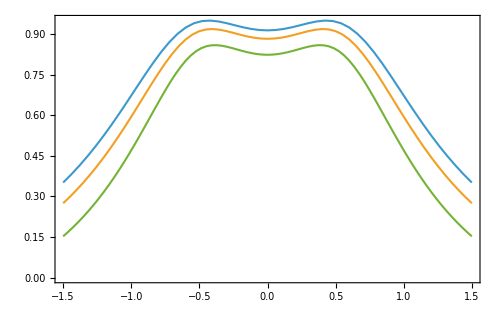

```mathematica
ListLinePlot[Evaluate@Table[Transpose[{vAllPlot[[k,All,1]]/dFieldLst[[k]],vAllPlot[[k,All,2]]}],{k,1,Length@vAllPlot}]]
```

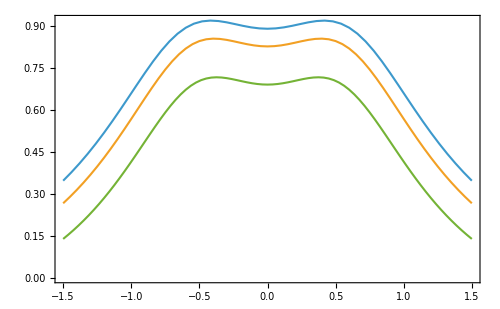

```mathematica
ListLinePlot[Evaluate@Table[Transpose[{vAllPlot[[k,All,1]]/dFieldLst[[k]],vAllPlot[[k,All,2]]}],{k,1,Length@vAllPlot}]]
```

#### Note: velocity values are already normalized (wrt structure velocity) in the BIM code.

```mathematica
vAllPlot//Dimensions
```

{3}

```mathematica
dFieldLst 3
```

{9.9999,12,15.9999}

```mathematica
Export["../outputData/BIMprocessed/uFieldD12.txt",Transpose[{vAllPlot[[2,All,1]]/dFieldLst[[2]],vAllPlot[[2,All,2]]}],"Table"]
```

../outputData/BIMprocessed/uFieldD12.txt

```mathematica
dFieldLst
```

{3.3333,4,5.3333}

```mathematica
16/3//N
```

5.33333

```mathematica
dLattice=6;
```

```mathematica
Graphics3D[{Cube[dLattice],Table[Sphere[{p1 dLattice/2,p2 dLattice/2,p3 dLattice/2},1],{p1,-1,1,2},{p2,-1,1,2},{p3,-1,1,2}],Opacity[0.7],
Cuboid[{-dLattice/2,-dLattice/2,dLattice/2},{dLattice/2,dLattice/2,dLattice/2+1}],
Cuboid[{-dLattice/2,-dLattice/2,-dLattice/2},{dLattice/2,dLattice/2,-dLattice/2-1}],Cuboid[{dLattice/2,-dLattice/2,-dLattice/2},{dLattice/2+1,dLattice/2,dLattice/2}],Cuboid[{-dLattice/2-1,-dLattice/2,-dLattice/2},{dLattice/2,dLattice/2,dLattice/2}],Cuboid[{-dLattice/2,dLattice/2,-dLattice/2},{dLattice/2,dLattice/2+1,dLattice/2}],Cuboid[{-dLattice/2,-dLattice/2,dLattice/2},{dLattice/2,-dLattice/2-1,dLattice/2}]},PlotRange->All]
```

-Graphics3D-

```mathematica
paramV={V1s->4/3 π,V1R->π(d-2)(0.5/3)^2};
```

```mathematica
phi=1-(8 V1s+12V1R)/(d^3+6 d^2+3π d+V1s)/.paramV
```

1-(1.0472 (-2+d)+(32 π)/3)/(6 d^2+d^3+(4 π)/3+3 d π)

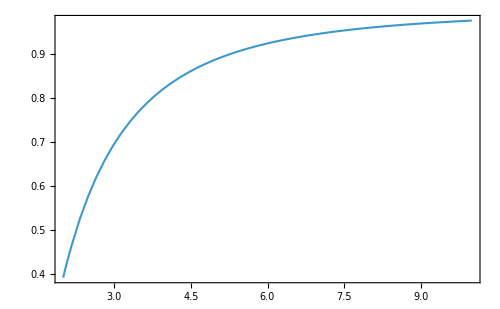

```mathematica
Plot[phi/.d->dd,{dd,2,10}]
```

```mathematica
dList
```

{2.5,3.,3.33,3.5,4.,4.5,5.,5.33,5.5,6.,6.5,7.}

```mathematica
VsND=8 +12 V1R/V1s/.paramV
```

8+0.25 (-2+d)

```mathematica
vNmrlz=Table[vFall[[k]]/VsND/.d->dList[[k]],{k,1,Length@dList}]
```

{0.291858,0.25331,0.232809,0.22373,0.200419,0.181746,0.166473,0.157799,0.153816,0.143196,0.134188,0.126475}

```mathematica
vNmrlz2=Table[vFall[[k]]/VsND^(2/3)/.d->dList[[k]],{k,1,Length@dList}]
```

{0.58674,0.511844,0.471981,0.454345,0.40902,0.372721,0.34304,0.326187,0.318462,0.297861,0.280409,0.265493}

```mathematica
phiList=Table[phi/.d->dl,{dl,dList}]
```

{0.579183,0.69543,0.748958,0.771534,0.823641,0.86063,0.887679,0.90168,0.907959,0.92349,0.935606,0.945209}

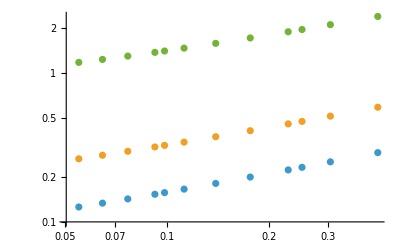

```mathematica
ListLogLogPlot[{Transpose[{1-phiList,vNmrlz}],Transpose[{1-phiList,vNmrlz2}],Transpose[{1-phiList,vFall}]}]
```

#### Faxen boundary correction factor:

```mathematica
dragFac[a_,Rcyl_]:=1-2.10443 a/Rcyl+2.08877 a^3/Rcyl^3-0.94813 a^5/Rcyl^5-1.372 a^6/Rcyl^6+3.87 a^8/Rcyl^8-4.19 a^10/Rcyl^10;
```

```mathematica
dragFac[1,25]
```

0.915956

```mathematica
mStr[1]
```

(92 π)/9

```mathematica
mStr[d_]:=(8+12 (1/6)^2(d-2));
```

```mathematica
NSolve[{x==mStr[d] 1/Uun,Uun==}]
```

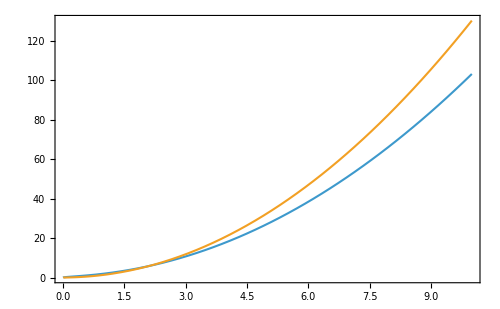

```mathematica
Plot[{x^2+x^(1/2),1.3 x^2+0.1 x^(1/3)},{x,0,10}]
```